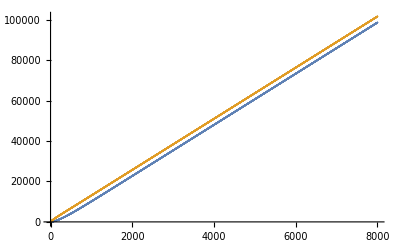

```mathematica
Module[{tf,T,R,k,ΔU,n,P,Ao,Vo,vo,Vi,rate,s,acceleration,velocity,x1,x2},
tf=8000;
T=700;(*K*)
R=8.314*10^-5;
k=0.1;
ΔU=0.416;
n=2;
P=5;
Ao=1;
Vo=Ao*R*T/P;
vo=1;
Vi=3000;

rate=-k*Exp[-ΔU/(R*T)];
s=NDSolve[{
A'[t]==rate*A[t]/V[t],
B'[t]==-n*rate*A[t]/V[t],
V'[t]==rate*(1-n)*A[t]/V[t]*(R*T)/P,
A[0]==Ao,
B[0]==0,
V[0]==Vo},{A,B,V},{t,0,tf}];

acceleration=Table[({V[t]/.s}-{V[t-1]/.s})/0.001,{t,1,tf}];
velocity=Table[Sum[acceleration[[i]],{i,1,t}],{t,1,tf}];
x1=Table[Sum[velocity[[i]]+vo,{i,1,t}],{t,1,tf}];
x2=Table[x1[[i]]+(Vi*({V[i-1]/.s}-{V[0]/.s})/({V[0]/.s})),{i,1,Length[x1]}];

ListPlot[{Flatten@x1,Flatten@x2}]
]
```

```mathematica
1/0.001
```

1000.